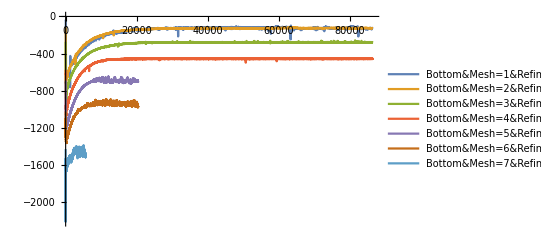

```mathematica
files = {
"Bottom&Mesh=1&Refinement=3.xlsx", 
"Bottom&Mesh=2&Refinement=3.xlsx",
"Bottom&Mesh=3&Refinement=3&Evaluation=1hour.xlsx",
"Bottom&Mesh=4&Refinement=2&Evaluation=17hour.xlsx",
"Bottom&Mesh=5&Refinement=2&Evaluation=17hour.xlsx",
"Bottom&Mesh=6&Refinement=2.xlsx",
"Bottom&Mesh=7&Refinement=2&Evaluation=28hour.xlsx"};
data=Import[NotebookDirectory[]<>#1][[3,13;;-1]]&/@files;
ListPlot[data,Joined->True,PlotLegends->files]
```